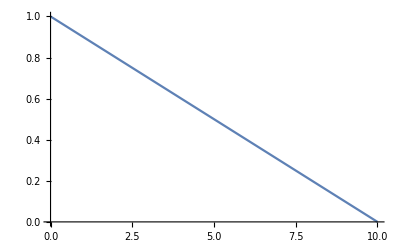

(G It)/L

0

-(G It)/L

0

```mathematica
(* ΟΜΟΙΟΜΟΡΦΗ ΣΤΡΕΨΗ *)
(* Υπολογισμός μητρώου δυσκαμψίας και επικόμβιων φορτίων από τις αρχικές συνθήκες *)
Clear[θx,mt,Mt]
mt[x_]:=0;
sol=DSolve[mt[x]==-G It θx''[x],θx[x],x];
θx[x_]:=Evaluate[θx[x]/.sol⟦1⟧]
sol=Solve[{θx[0]==1,θx[L]==0},{C[1],C[2]}];
θx[x_]:=Evaluate[FullSimplify[θx[x]/.sol⟦1⟧]]
Mt[x_]:=FullSimplify[-G It θx'[x]]
Mw[x_]:=0
Plot[θx[x]/.{L->10,G->76000000000,It->0.00001},{x,0,10}]
k2=Mt[0]
k4=Mw[0]
k6=-Mt[L]
k8=Mw[L]
(* ΠΡΟΣΟΧΗ!!! Οι επικόμβιες δυνάμεις που προκύπτουν από το κατανεμημένο έχουν αντίθετο πρόσημο F0'=-F0. Η μητρωϊκή σχέση είναι F=K.X-F0 *)
```